```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
plotopts = {Frame->True, BaseStyle->{ FontSize->15} , ImageSize->500};
SetOptions[{Plot,ListPlot}, plotopts];
mc2N = 0.511 10^6;
eChargeN=1.6 10^-19;
cLightN=299792458.;
```

## Line test

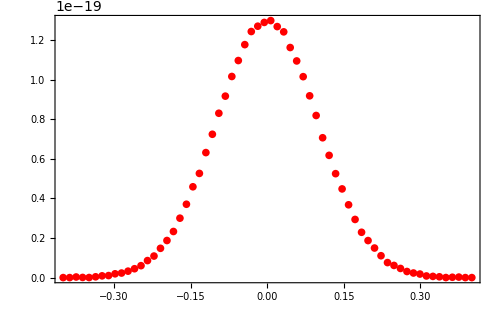

```mathematica
chargedat1=Import["charge_z.dat", "Table"];
gEzline=ListPlot[{1000#⟦1⟧, 10^-6#⟦2⟧}&/@chargedat1, PlotStyle->Red]
```

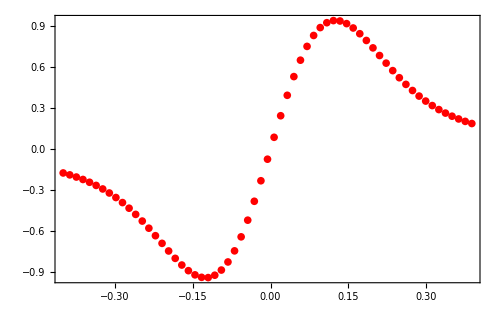

```mathematica
zdat1=Import["field_z_Ez.dat", "Table"];
gEzline=ListPlot[{1000#⟦1⟧, 10^-6#⟦2⟧}&/@zdat1, PlotStyle->Red]
```

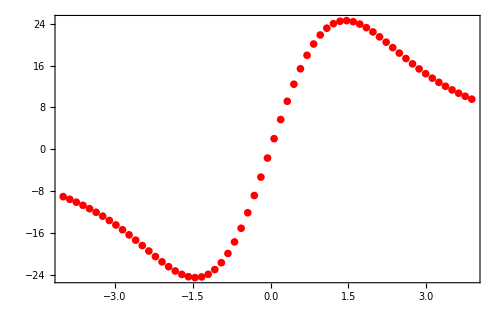

```mathematica
xdat1=Import["field_x_Ex.dat", "Table"];
gExline=ListPlot[{1000#⟦1⟧, 10^-6#⟦2⟧}&/@xdat1, PlotStyle->Red]
```

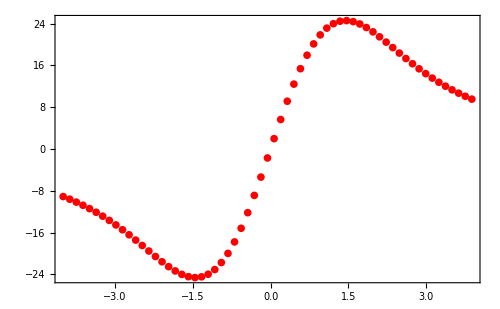

```mathematica
ydat1=Import["field_y_Ey.dat", "Table"];
gEyline=ListPlot[{1000#⟦1⟧, 10^-6#⟦2⟧}&/@ydat1, PlotStyle->Red]
```

## Analytic calc (See Stupakov)

7.17103

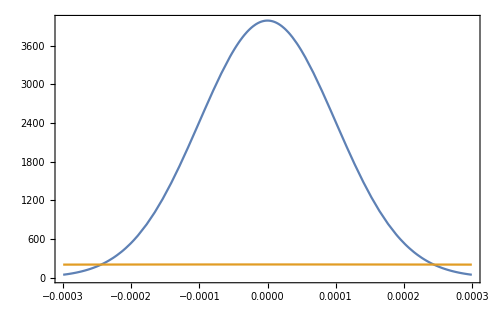

```mathematica
λG[z_, σ_]:=1/(√(2 π)σ)Exp[(- 1)/2(z/σ)^2];
sl={σ->.0001, a ->.001};
Eref = 10 10^6;
cpzref =√(Eref^2-mc2N^2);
γ =Eref /mc2N; 
βref = √(1-1/γ^2);
σz=σ/.sl;
σx=a/.sl;
σy=σx;
σzrest = γ σz;

charge = 1000 10^-12(*C*);
prefactor = cLightN^2 10^-7 √(2/π)charge


Plot[{λG[z, σz], λG[z, σzrest]}, {z, -3σz,3σz}]
```

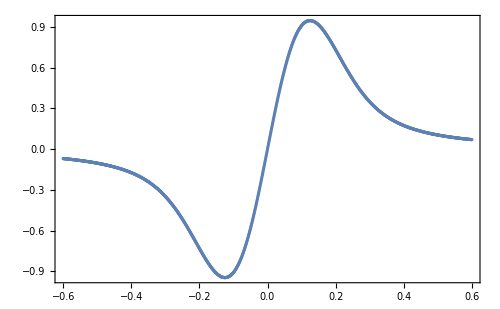

```mathematica
Clear[λ];
(*Line along z (x=0, y=0)*)
Ezintegrandλ[λ_,z_]:=(z  λ^2)/(1+(λ σzrest)^2)Exp[(-(λ z)^2)/(2(λ^2 σzrest^2 + 1))] 1/(√((λ^2 σx^2 + 1)(λ^2 σy^2 + 1)(λ^2 σzrest^2 + 1)));
Ezdat=Table[{z,NIntegrate[Ezintegrandλ[λλ, z], {λλ, 0,∞}]}, {z,-6σzrest,6σzrest, σzrest/100}];//Quiet
gAnalyticZ = Show[ListPlot[{1000#⟦1⟧/γ, 10^-6 prefactor#⟦2⟧}&/@Ezdat]]
```

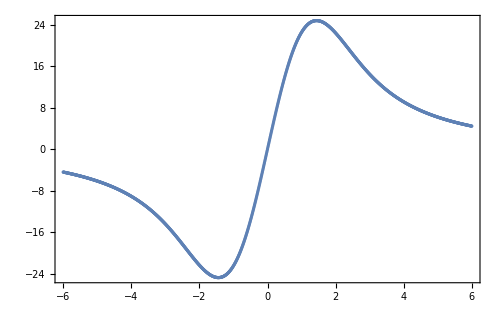

```mathematica
Clear[λ];
(*Line along x (z=0, y=0)*)
Exintegrandλ[λ_,x_]:=(x  λ^2)/(1+(λ σx)^2)Exp[(-(λ x)^2)/(2(λ^2 σx^2 + 1))] 1/(√((λ^2 σx^2 + 1)(λ^2 σy^2 + 1)(λ^2 σzrest^2 + 1)));
Exdat=Table[{x,NIntegrate[Exintegrandλ[λλ, x], {λλ, 0,∞}]}, {x,-6σx,6σx, σx/100}];//Quiet
gAnalyticX = Show[ListPlot[{1000#⟦1⟧,  γ 10^-6 prefactor #⟦2⟧}&/@Exdat]]
```

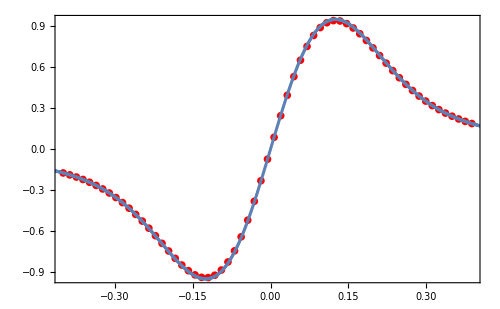

```mathematica
Show[gEzline, gAnalyticZ]
```

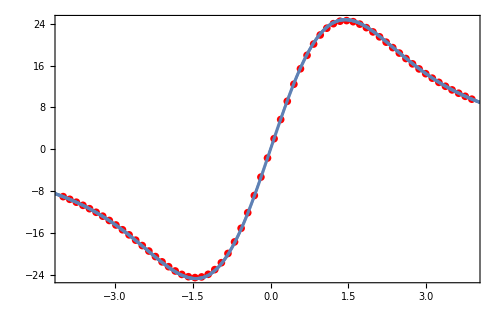

```mathematica
Show[gExline, gAnalyticX ]
```

```mathematica
Clear[λ];
(*Line along y (z=0, x=0)*)
Eyintegrandλ[λ_,y_]:=(y  λ^2)/(1+(λ σy)^2)Exp[(-(λ y)^2)/(2(λ^2 σy^2 + 1))] 1/(√((λ^2 σx^2 + 1)(λ^2 σy^2 + 1)(λ^2 σzrest^2 + 1)));
Eydat=Table[{y,NIntegrate[Eyintegrandλ[λλ, y], {λλ, 0,∞}]}, {y,-6σy,6σy, σy/100}];//Quiet
gAnalyticY = Show[ListPlot[{1000#⟦1⟧,  γ 10^-6 prefactor #⟦2⟧}&/@Eydat]]
```

-Graphics-

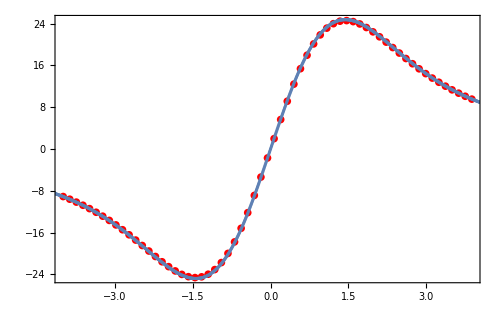

```mathematica
Show[gEyline, gAnalyticY ]
```

## Astra comparison

```mathematica
adatX = Import["astra/astra.Xemit.001", "Table"];
adatY = Import["astra/astra.Yemit.001", "Table"];
adatZ = Import["astra/astra.Zemit.001", "Table"]
```

{{3.6409×10^-16,2.0123×10^-22,9.489,0.1,0.000010233,9.9742×10^-7,-6.1668×10^-17},{1.,3.34,9.5021,0.14762,315.11,11.005,306.17}}

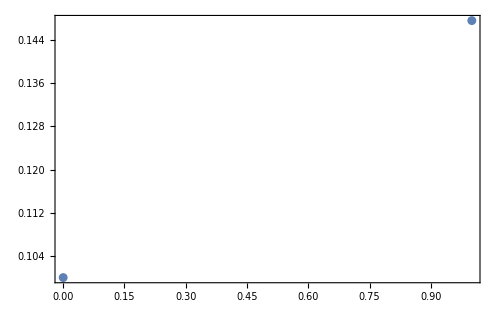

```mathematica
ListPlot[{#⟦1⟧, #⟦4⟧}&/@adatZ, PlotRange->All]
```

## Bmad

{1.02011×10^-9,6.16852×10^-11,1.,-0.00154051,-0.00147752,9.98696×10^6,3.34002,0.,1,5}

10

{0.00209516,0.00209496,0.000147548,18456.4,18453.5,315176.}

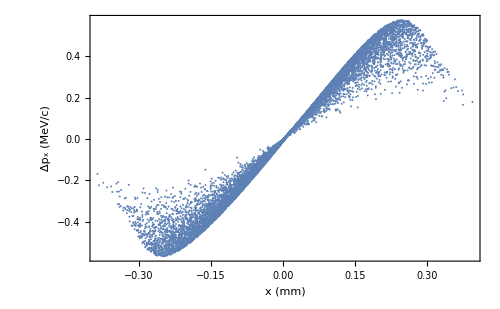

```mathematica
allbpart  =Import["end.particles_10k", "Table"];
bpart1 = allbpart[[1]]
Length[bpart1]
(*bpart = RandomSample[allbpart[[2;;]], 10000];*)
bpart =Flatten[ {#⟦1;;5⟧, #⟦6⟧+bpart1⟦6⟧ - cpzref}] &/@allbpart[[2;;10001]];

StandardDeviation/@Transpose[ bpart ]
ListPlot[{1000#⟦3⟧,10^-6#⟦6⟧}&/@bpart, PlotRange->All,FrameLabel-> { "x (mm)", "Δp_x (MeV/c)"}]
```

```mathematica
StandardDeviation/@Transpose[ bpart ⟦2;;⟧]
```

{0.00209505,0.00209506,0.000147555,18454.8,18454.4,315192.}

```mathematica
Min/@Transpose[ bpart ⟦2;;⟧]
```

{-0.00476547,-0.0049498,-0.000386227,-37590.9,-37534.3,-568410.}

```mathematica
Max/@Transpose[ bpart ⟦2;;⟧]
```

{0.00469911,0.00489886,0.000393686,37395.4,37456.9,574902.}

```mathematica
(* Zero charge*)
allbpartOFF =Import["off/end.particles_10k", "Table"];
bpart1OFF = allbpartOFF[[1]]
bpartOFF =Flatten[ {#⟦1;;5⟧, #⟦6⟧+bpart1OFF⟦6⟧ - cpzref}] &/@allbpartOFF[[2;;10001]];
```

{9.99998×10^-10,-2.15444×10^-15,1.,-1.90846×10^-11,-3.02021×10^-11,9.98694×10^6,3.34,0.,1,5}

## Astra

```mathematica
allapart  =Import["astra/astra.0100.001_10k", "Table"];
apart1=allapart [[1]]
StandardDeviation/@Transpose[ allapart ⟦2;;⟧]
```

{3.8837×10^-10,3.0896×10^-10,1.,0.0086475,0.0072261,9.978×10^6,3.34,0.,1,5}

{0.00209447,0.00209447,0.000147599,18452.3,18451.7,315630.,0.,0.,0,0}

```mathematica
apart = Flatten[ {#⟦1;;5⟧, #⟦6⟧+apart1⟦6⟧ - cpzref}] &/@allapart[[2;;10001]]
```

{{8.9623×10^-9,7.8492×10^-9,-1.3103×10^-10,0.10007,0.087627,-8935.79},{-0.0018422,-0.0018404,0.00012125,-18656.,-18633.,338485.},{0.0019251,0.0019232,-0.00012378,19029.,19006.,-311985.},9994,{-0.00059322,0.002558,0.00006551,-6134.8,26434.,191295.},{0.003052,-0.0011045,-0.0001738,26400.,-9552.4,-372255.},{-0.00064706,-0.00022971,0.00022431,-6212.4,-2204.1,562225.}}
 |  |  |  |

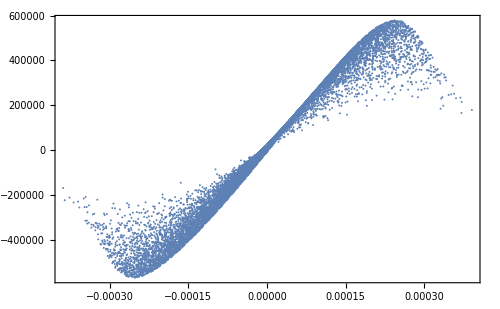

```mathematica
ListPlot[{#⟦3⟧, #⟦6⟧}&/@apart]
```

## Compare

```mathematica
bdat = Import["temp_diagnostics.dat", "Table"]
```

{{step,ds,sigma_x,sigma_y,sigma_z},{0.1,0.00101357,0.00101357,0.000100586},{0.2,0.00105387,0.00105387,0.000102322},{0.3,0.00111963,0.00111963,0.000105149},{0.4,0.00120885,0.00120885,0.000108983},{0.5,0.00131901,0.00131901,0.000113723},{0.6,0.0014474,0.0014474,0.000119264},{0.7,0.00159142,0.00159142,0.000125507},{0.8,0.0017487,0.0017487,0.000132358},{0.9,0.00191723,0.00191722,0.000139736},{1.,0.00209528,0.00209527,0.00014757}}

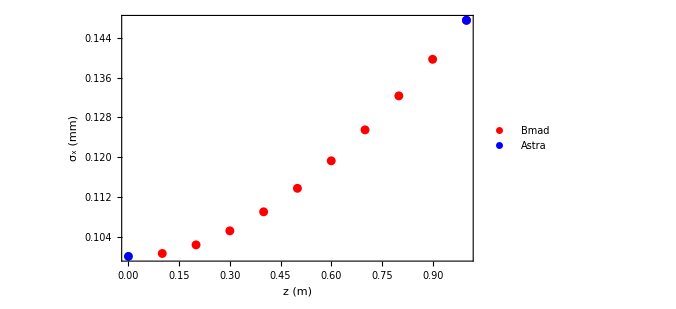

```mathematica
ListPlot[
{
Legended[{#⟦1⟧,1000  #⟦4⟧}&/@bdat[[2;;]], "Bmad"],
Legended[{#⟦1⟧,#⟦4⟧}&/@adatZ, "Astra"]
}, PlotStyle->{{Large,Red}, Blue}, FrameLabel->{"z (m)", "σ_x (mm)"}]
```

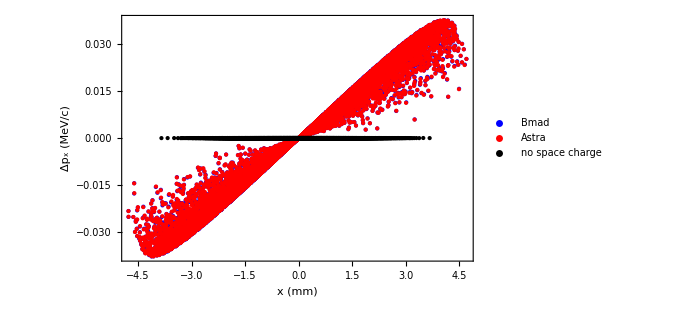

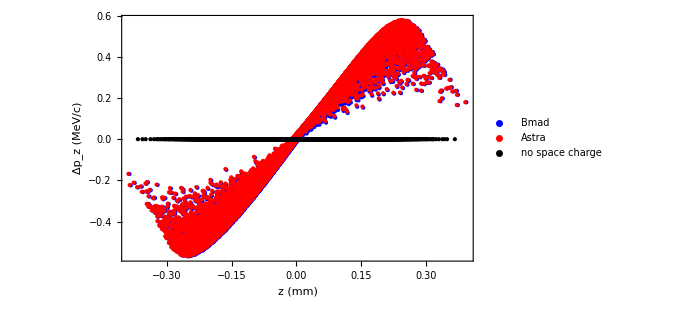

```mathematica
myf = {1000#⟦3⟧, 10^-6 #⟦6⟧}&;
label={"z (mm)", "Δp_z (MeV)"};
legend = PointLegend[{Blue, Red, Black},{"Bmad", "Astra", "no space charge"}, LegendMarkerSize->15];
Compare[f_Function, label_]:=
ListPlot[
{
f/@bpart,
f/@apart,
f/@bpartOFF 

}, PlotStyle->{{PointSize[Small],Blue},{PointSize[Tiny],  Red}, {PointSize[Small], Black}}, FrameLabel->label,  PlotRange->All,FrameStyle->Directive[Black], ImageSize->500, BaseStyle->{FontSize->15}, Epilog->Inset[legend,Scaled[ {0.2,0.8}]]];
gBAx = Compare[ ({1000#⟦1⟧, 10^-6 #⟦4⟧}&), { "x (mm)", "Δp_x (MeV/c)"}]
gBAz = Compare[ ({1000#⟦3⟧, 10^-6 #⟦6⟧}&), { "z (mm)", "Δp_z (MeV/c)"}]
```

## ImpactZ

```mathematica
(*
ImpactZ Phase space coordinates are stupid:

x * omega/c, cPx/mc2, y * omega/c, omega*t, (E0 - E)/mc2 , q/m = -1/mc2, q_macro (C), particle ID

*)
```

### Make particles

```mathematica
(*Pick omega = c for simplicity. *)
omega = 299792548.;
f = omega/(2 π)
```

4.77135×10^7

```mathematica
rawadat0 = Import["beginning_astra.particles", "Table"];
adat0ref = rawadat0[[1]];
adat0 = rawadat0[[2;;]];
(*Set particle ID *)
Do[adat0 [[i,9]] = i, {i,Length[adat0]}]
```

```mathematica
StandardDeviation/@Transpose[adat0]
```

{0.001,0.001,0.0001,9.98694,9.98694,0.00998694,7.50941×10^-22,0.,500 √(1000001/3),0}

```mathematica
Clear[AstraToImpactZ];
AstraToImpactZ[{x_, y_, z_, cpx_, cpy_, cpz_, tns_, qnC_, id_,stat_}, zref_, cpzref_]:=Module[{},
{x*(omega/cLightN), cpx/mc2N,
y*(omega/cLightN), cpy/mc2N, 
-(z+zref) / (omega/cLightN) /βref, ( Eref- Sqrt[ mc2N^2 + cpx^2+ cpy^2+ (cpzref + cpz)^2])/mc2N,
-1/mc2N, qnC*10^-9,
id}

];
impactz0 = AstraToImpactZ[#,adat0ref [[3]],adat0ref [[6]]]&/@adat0;
```

```mathematica
(*Check total charge*)
Total[impactz0 [[All,8]]]/10^-9 "nC"
```

1. nC

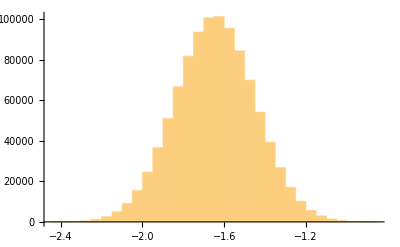

```mathematica
Histogram[impactz0 [[All,6]]]
```

```mathematica
Export["impactz/partcl.data", {Length[impactz0], 0, 0}~Join~impactz0, "Table"]
```

impactz/partcl.data

### Import Results

```mathematica
basedir = "impactz/";
rawpdat = Import[basedir<>"fort.99_10k", "Table"];

charge = Total[rawpdat[[All,8]]]; Print[charge/10^-9, "nC"]
pdat = {omega /cLightN #⟦1⟧ ,omega /cLightN #⟦3⟧, (#⟦5⟧cLightN/omega) βref ,
 mc2N#⟦2⟧,
 mc2N#⟦4⟧,
 Sqrt[(mc2N#⟦6⟧ + Eref)^2-( mc2N#⟦2⟧)^2-( mc2N#⟦4⟧)^2-mc2N^2] , #⟦6⟧/omega}&/@rawpdat[[1;;10000]];
StandardDeviation/@Transpose[pdat]
```

0.01nC

{0.0020885,0.00208851,0.000147347,18366.2,18365.8,314089.,2.04758×10^-9}

```mathematica
(*Beam 1:Charge averaged over 1 rf period=Q*(reference frequency)*)
charge  * f
```

0.000477135

```mathematica
imeans=Mean/@Transpose[pdat]
```

{-6.60448×10^-7,-2.18277×10^-7,3.38496×10^-6,-3.27488,1.9051,9.9869×10^6,9.71813×10^-14}

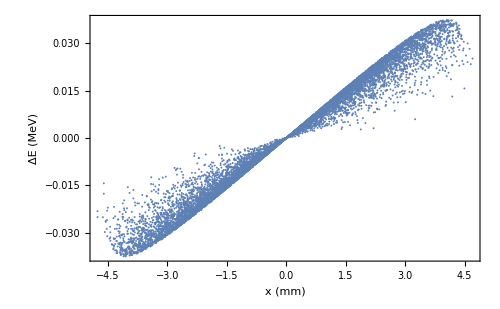

```mathematica
idatx={1000#⟦1⟧, 10^-6#⟦4⟧}&/@pdat;
ListPlot[idatx, PlotRange->All, FrameLabel->{"x (mm)", "ΔE (MeV)"}]
```

```mathematica
imeans[[6]]
```

9.9869×10^6

```mathematica
pdat0 =Flatten[ {#[[1;;5]], #[[6]]-cpzref}]&/@pdat;
```

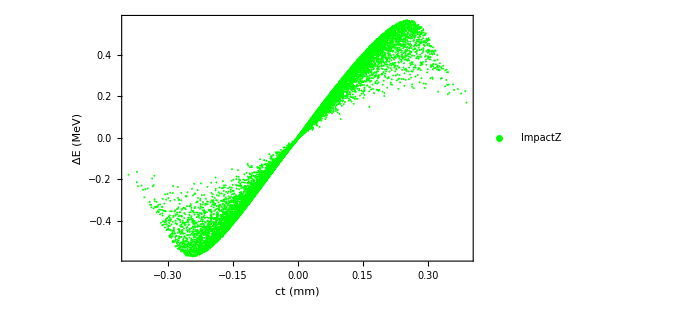

```mathematica
idatz={1000#⟦3⟧, 10^-6(#⟦6⟧-cpzref)}&/@pdat;


gIz = ListPlot[Legended[idatz,"ImpactZ"], PlotRange->All, FrameLabel->{"ct (mm)", "ΔE (MeV)"}, PlotStyle->Green]
```

```mathematica
(*
Old:
ListPlot[Legended[{1000#⟦1⟧/γ, .001 10^-6 prefactor#⟦2⟧}&/@Ezdat, "Analytic on-axis"]*)
```

OptionValue::nodef: Unknown option Joined for Graphics.

OptionValue::nodef: Unknown option PlotStyle for Graphics.

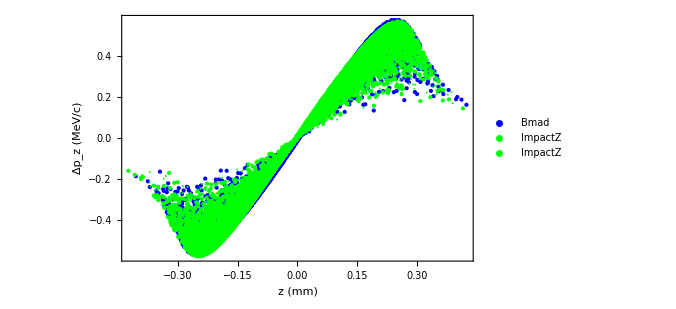

```mathematica
Show[ gz, gIz, Joined->True, PlotStyle->Black]
```

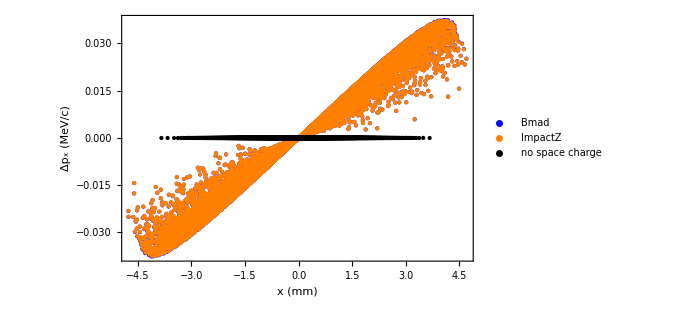

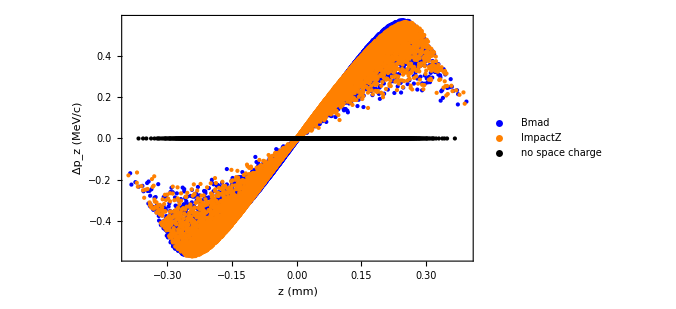

```mathematica
myf = {1000#⟦3⟧, 10^-6 #⟦6⟧}&;
label={"z (mm)", "Δp_z (MeV)"};
legend = PointLegend[{Blue, Orange, Black},{"Bmad", "ImpactZ" ,"no space charge"}, LegendMarkerSize->15];
Compare[f_Function, label_]:=
ListPlot[

{
f/@bpart,
f/@pdat0, 
f/@bpartOFF

}, PlotStyle->{{PointSize[Small],Blue},{PointSize[Tiny], Orange},{PointSize[Small], Black}}, FrameLabel->label, PlotRange->All, ImageSize->500, FrameStyle->Directive[Black],BaseStyle->{FontSize->15}, Epilog->Inset[legend,Scaled[ {0.2,0.8}]]];
gBIx = Compare[ ({1000#⟦1⟧, 10^-6 #⟦4⟧}&), { "x (mm)", "Δp_x (MeV/c)"}]
gBIz = Compare[ ({1000#⟦3⟧, 10^-6 #⟦6⟧}&), { "z (mm)", "Δp_z (MeV/c)"}]
```

## Export

```mathematica
Export["bmad_astra_px.pdf", gBAx]
Export["bmad_astra_pz.pdf", gBAz]
```

bmad_astra_px.pdf

bmad_astra_pz.pdf

```mathematica
Export["bmad_impactz_px.pdf", gBIx]
Export["bmad_impactz_pz.pdf", gBIz]
```

bmad_impactz_px.pdf

bmad_impactz_pz.pdf

## GPT

```mathematica
1.0/ cLightN
```

3.33564×10^-9

```mathematica
rgdat = Import["gpt/gpt.out.txt", "Table"];
```

```mathematica
step =5;
ix1=Position[rgdat, "time"][[step,1]]
ix2 = Position[rgdat, "time"][[step+1,1]]
rgdat[[ix1;;ix1+1]]
```

40015

50018

{{time,3.33564×10^-9},{x,y,z,G,Bx,By,Bz,rxy,m,q,nmacro,rmacro,ID,fEx,fEy,fEz,fBx,fBy,fBz}}

```mathematica
rgdat[[ix1;;ix1+1]]
```

{{time,3.33564×10^-9},{x,y,z,G,Bx,By,Bz,rxy,m,q,nmacro,rmacro,ID,fEx,fEy,fEz,fBx,fBy,fBz}}

```mathematica
rgdat1=RandomSample[rgdat[[ix1+2;;ix2-2]], 10000];
gpart ={#⟦1⟧,#[[2]], #[[3]],  mc2N#⟦4⟧#⟦5⟧,mc2N#⟦4⟧#⟦6⟧, mc2N#⟦4⟧#⟦7⟧, #⟦14⟧, #⟦15⟧, #⟦16⟧ }&/@rgdat1;
gmeans = Mean/@Transpose[gpart ]
```

{-1.59937×10^-6,-1.57151×10^-6,0.998692,-2.57296,-2.04873,1.×10^7,-81.058,-54.7699,-26.6919}

```mathematica
Total[rgdat1[[All,11]]]eChargeN  / 10^-9"nC"
```

0.998634 nC

```mathematica
Mean[rgdat1[[All,4]]]mc2N /10^6"MeV"
```

10.0131 MeV

```mathematica
gsigmas = StandardDeviation/@Transpose[gpart ]
```

{0.00209678,0.0020966,0.000143572,18563.8,18569.1,294554.,2.98434×10^6,2.98449×10^6,136128.}

```mathematica
gpart0 =( #-gmeans)&/@ gpart;
Mean/@Transpose[gpart0]
```

{1.38778×10^-20,-8.46545×10^-20,5.36793×10^-17,-2.56114×10^-13,3.72529×10^-13,3.91025×10^-9,7.7486×10^-11,1.18464×10^-10,-1.67638×10^-12}

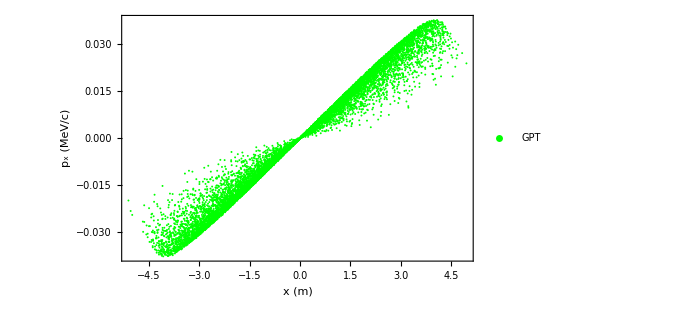

```mathematica
Show [  ListPlot[
Legended[{1000#⟦1⟧,10^-6 #[[4]]}&/@gpart, "GPT"], PlotRange->All,PlotStyle->Green, FrameLabel->{"x (m)", "p_x (MeV/c)"}]]
```

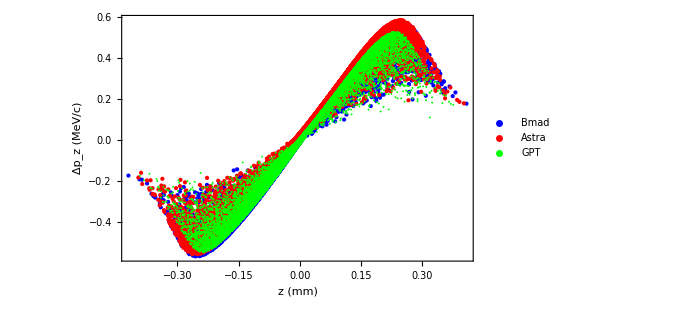

```mathematica
Show[ gz, ListPlot[
Legended[{1000#⟦3⟧,10^-6#[[6]]}&/@gpart0, "GPT"], PlotRange->All,PlotStyle->Green, FrameLabel->{"z (m)", "p_z (MeV/c)"}]]
```